```mathematica
$Assumptions=m>0&&En>0&&ω>0;
```

```mathematica
p[x_]:=√(2m(En-V[x]))
```

```mathematica
V[x_]:=1/2 m ω^2 x^2
```

```mathematica
x2=1/ω √((2En)/m);
```

```mathematica
n=3;
```

```mathematica
En=(2n-1/2)ℏ ω;
```

```mathematica
ℏ=m=ω=1;
```

```mathematica
ψ1[x_]:=2/(√p[x])Sin[1/ℏ NIntegrate[p[xp],{xp,x,x2}]+π/4]
```

```mathematica
ψ3[x_]:=1/(√Abs[p[x]])Exp[-1/ℏ NIntegrate[Abs[p[xp]],{xp,x2,x}]]
```

```mathematica
α=((2m)/ℏ^2 V'[x2])^(1/3);
```

```mathematica
ψ2[x_]:=√((4π)/(α ℏ))AiryAi[α(x-x2)]
```

```mathematica
ψWKB[x_]:=If[x<0.85x2,ψ1[x],If[x<1.15x2,ψ2[x],ψ3[x]]]
```

```mathematica
norm=1/(√NIntegrate[ψWKB[x]^2,{x,0,2x2}]);
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.82421}. NIntegrate obtained 3.16122 and 0.000452179 for the integral and error estimates.

```mathematica
ψexact[n_,x_]:=√2((m ω)/(π ℏ))^(1/4)1/(√(2^n n!))HermiteH[n,√((m ω)/ℏ)x]Exp[-1/2(√((m ω)/ℏ)x)^2]
```

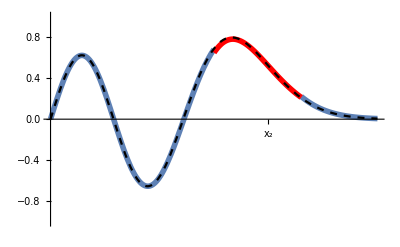

```mathematica
Show[Plot[norm ψ1[x],{x,0,.75x2},PlotRange->{{0,1.5x2},{-1,1}},Ticks->{{{x2,"x_2"}},None},PlotStyle->Thickness[0.01]],Plot[norm ψ3[x],{x,1.15x2,1.5x2},PlotRange->All,PlotStyle->Thickness[0.01]],Plot[norm ψ2[x],{x,.75x2,1.15x2},PlotRange->{{0,2x2},{-2,2}},PlotStyle->{Red,Thickness[0.01]}],Plot[ψexact[2n-1,x],{x,0,1.5x2},PlotStyle->{Black,Dashed}]]
```